```mathematica
Clear["`*"]
```

Defino los valores de las constantes:

```mathematica
si=0;
```

```mathematica
ωi=35;
```

```mathematica
li=2;
```

```mathematica
mi=1;
```

```mathematica
ωgi=ωi;
```

```mathematica
c=2.99*10^8;
```

```mathematica
rs=1;
```

Definimos los parámetros:

```mathematica
α3=(si+1);
```

```mathematica
β3=2 I ωi;
```

```mathematica
γ3=1+2 si;
```

```mathematica
δ3=1-2 I ωi;
```

```mathematica
q3=si(si+1)-li(li+1);
```

## Considerado la ecuación diferencial trasladada (el cambio de variable efectuado fue ).

```mathematica
soli23=DSolve[ y''[x]+(γ3/(x-1)+δ3/x+β3)y'[x]-(α3 β3 (1-x)-q3)/(x(x-1))y[x]==0,y[x],x];
```

Definimos una función para la ecuación diferencial trasladada:

```mathematica
Hu3=y[x]/. First[soli23]/.{C[2] ->0,C[1]->1,x->1-r[t]} ;
```

```mathematica
HuPrime3=D[Hu3,r[t]];
```

```mathematica
(*Definir las condiciones iniciales*)
r0=5rs;
θ0=Pi;
ϕ0=Pi/2;
```

```mathematica
v0=v0=N[r0+rs Log[Abs[(r0/rs)-1]]]
```

6.38629

```mathematica
σ=N[1/(2ωgi)]
```

0.0142857

## Proceso de Ito:

Pre-definir, valores de Heun:

```mathematica
ReHu3=Re[Hu3];
ImHu3=Im[Hu3];
ReHuPrime3=Re[HuPrime3];
ImHuPrime3=Im[HuPrime3];
```

Proceso de Ito optimizado:

```mathematica
EFITO=ItoProcess[{ⅆr[t]==(2 σ ((1-1/r[t])( (ReHuPrime3(ReHu3-ImHu3)+ImHuPrime3(ImHu3+ReHu3))/((ReHu3)^2+(ImHu3)^2))-ωi))ⅆt+Sqrt[2 σ] ⅆw1[t],ⅆv[t]==(2σ ((ReHuPrime3(ReHu3-ImHu3)+ImHuPrime3(ImHu3+ReHu3))/((ReHu3)^2+(ImHu3)^2)))ⅆt+Sqrt[2 σ] ⅆw2[t]},{r[t],v[t]},{{r,v},{r0,v0}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}];
```

```mathematica
soluEF =RandomFunction[EFITO,{0,1,0.01},7,Method->"StochasticRungeKutta"];
```

```mathematica
traTime=soluEF["Paths"][[1,All,1]];
```

```mathematica
traR1=soluEF["Paths"][[1,All,2,1]];
```

```mathematica
traR2=soluEF["Paths"][[2,All,2,1]];
```

```mathematica
traR3=soluEF["Paths"][[3,All,2,1]];
```

```mathematica
traR4=soluEF["Paths"][[4,All,2,1]];
```

```mathematica
traR5=soluEF["Paths"][[5,All,2,1]];
```

```mathematica
traR6=soluEF["Paths"][[6,All,2,1]];
```

```mathematica
traR7=soluEF["Paths"][[7,All,2,1]];
```

```mathematica
traV1=soluEF["Paths"][[1,All,2,2]];
```

```mathematica
traV2=soluEF["Paths"][[2,All,2,2]];
```

```mathematica
traV3=soluEF["Paths"][[3,All,2,2]];
```

```mathematica
traV4=soluEF["Paths"][[4,All,2,2]];
```

```mathematica
traV5=soluEF["Paths"][[5,All,2,2]];
```

```mathematica
traV6=soluEF["Paths"][[6,All,2,2]];
```

```mathematica
traV7=soluEF["Paths"][[7,All,2,2]];
```

```mathematica
mean=TimeSeriesThread[Mean,soluEF];
```

```mathematica
R1=Transpose[{traTime,traR1}];
```

```mathematica
R2=Transpose[{traTime,traR2}];
```

```mathematica
R3=Transpose[{traTime,traR3}];
```

```mathematica
R4=Transpose[{traTime,traR4}];
```

```mathematica
R5=Transpose[{traTime,traR5}];
```

```mathematica
R6=Transpose[{traTime,traR6}];
```

```mathematica
R7=Transpose[{traTime,traR7}];
```

```mathematica
T1=Transpose[{traTime,traV1}];
```

```mathematica
T2=Transpose[{traTime,traV2}];
```

```mathematica
T3=Transpose[{traTime,traV3}];
```

```mathematica
T4=Transpose[{traTime,traV4}];
```

```mathematica
T5=Transpose[{traTime,traV5}];
```

```mathematica
T6=Transpose[{traTime,traV6}];
```

```mathematica
T7=Transpose[{traTime,traV7}];
```

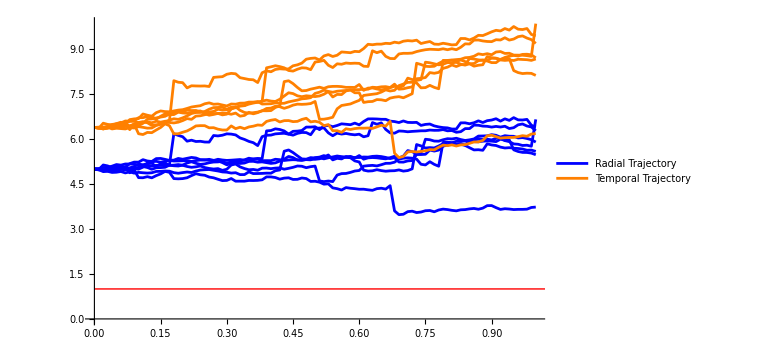

```mathematica
Result3=ListLinePlot[{R1,T1,R2,R3,R4,R5,R6,R7,T2,T3,T4,T5,T6,T7},AxesLabel->{Style["",Bold,Black],Style["",Bold,Black]},LabelStyle->Directive[Bold,Medium],PlotRange->All,ImageSize->Large,PlotStyle->{Blue,Orange,Blue,Blue,Blue,Blue,Blue,Blue,Orange,Orange,Orange,Orange,Orange,Orange},PlotLegends->Placed[{Style["Radial Trajectory ",Bold,Black],Style["Temporal Trajectory ",Bold,Black]},Right],Epilog->{Red,Thick,Line[{{0,1},{5,1}}]}]
```

Recuerde, de manera general, que el  resulta siendo nuestro  en mathematica.

```mathematica
Export["C:\\Users\\Juan Sebastian\\Documents\\Cinvestav\\Tesis\\Tesis\\stochastic differential equations\\Velocidades\\Grafica parametrica, l=1,m=0\\Graficas\\Graficas sin unidades\\Variando omega0\\omega 10000\\r y v vs tau\\grafica2(7trayec-25s).PNG",Result3,"PNG",ImageResolution->300];
```

## Trayectorias:

```mathematica
Tr1=Transpose[{traV1,traR1}];
```

```mathematica
Tr2=Transpose[{traV2,traR2}];
```

```mathematica
Tr3=Transpose[{traV3,traR3}];
```

```mathematica
Tr4=Transpose[{traV4,traR4}];
```

```mathematica
Tr5=Transpose[{traV5,traR5}];
```

```mathematica
Tr6=Transpose[{traV6,traR6}];
```

```mathematica
Tr7=Transpose[{traV7,traR7}];
```

## Gráfica sin transformación:

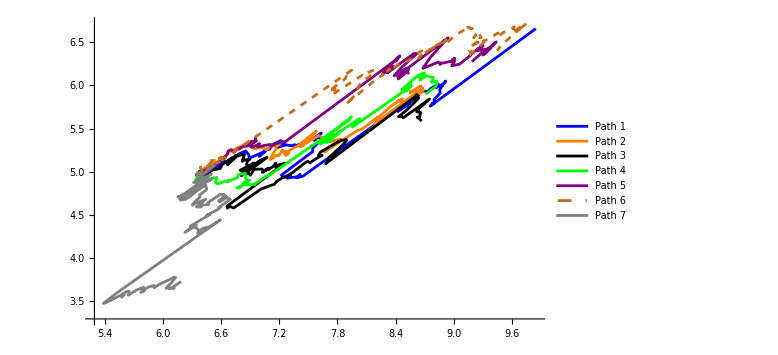

```mathematica
Result4=ListLinePlot[{Tr1,Tr2,Tr3,Tr4,Tr5,Tr6,Tr7},AxesLabel->{Style["",Bold,Black],Style["",Bold,Black]},LabelStyle->Directive[Bold,Medium],
PlotRange->All,ImageSize->Large, PlotStyle->{Blue,Orange,Black,Green,Purple,Dashed,Gray},PlotLegends->Placed[{Style["Path 1",Bold,Black],Style["Path 2",Bold,Black],Style["Path 3",Bold,Black],Style["Path 4",Bold,Black],Style["Path 5",Bold,Black],Style["Path 6",Bold,Black],Style["Path 7",Bold,Black]},Right],Epilog->{Red,Thick,Line[{{0,1},{3,1}}]}]
```

```mathematica
Export["C:\\Users\\Juan Sebastian\\Documents\\Cinvestav\\Tesis\\Tesis\\stochastic differential equations\\Velocidades\\Grafica parametrica, l=1,m=0\\Graficas\\Graficas sin unidades\\Variando omega0\\omega 10000\\r vs v\\grafica2(7trayec-25s).PNG",Result4,"PNG",ImageResolution->300];
```

```mathematica
(*Define the function to compute ct from cv and r*)
ct[cv_,r_]:=cv-r-rs Log[Abs[(r/rs)-1]]
```

```mathematica
(*Apply the function to each element of the list Tr1*)
TraT1=ct@@@Tr1;
```

```mathematica
TraT2=ct@@@Tr2;
```

```mathematica
TraT3=ct@@@Tr3;
```

```mathematica
TraT4=ct@@@Tr4;
```

```mathematica
TraT5=ct@@@Tr5;
```

```mathematica
TraT6=ct@@@Tr6;
```

```mathematica
TraT7=ct@@@Tr7;
```

```mathematica
Tr11=Transpose[{TraT1,traR1}];
```

```mathematica
Tr22=Transpose[{TraT2,traR2}];
```

```mathematica
Tr33=Transpose[{TraT3,traR3}];
```

```mathematica
Tr44=Transpose[{TraT4,traR4}];
```

```mathematica
Tr55=Transpose[{TraT5,traR5}];
```

```mathematica
Tr66=Transpose[{TraT6,traR6}];
```

```mathematica
Tr77=Transpose[{TraT7,traR7}];
```

```mathematica
(*Define the function to compute ct from cv and r*)
ct[cv_,r_]:=cv-r-rs Log[Abs[(r/rs)-1]]
```

```mathematica
(*Apply the function to each element of the list Tr1*)
TraT1=ct@@@Tr1;
```

```mathematica
TraT2=ct@@@Tr2;
```

```mathematica
TraT3=ct@@@Tr3;
```

```mathematica
TraT4=ct@@@Tr4;
```

```mathematica
TraT5=ct@@@Tr5;
```

```mathematica
TraT6=ct@@@Tr6;
```

```mathematica
TraT7=ct@@@Tr7;
```

```mathematica
Tr11=Transpose[{TraT1,traR1}];
```

```mathematica
Tr22=Transpose[{TraT2,traR2}];
```

```mathematica
Tr33=Transpose[{TraT3,traR3}];
```

```mathematica
Tr44=Transpose[{TraT4,traR4}];
```

```mathematica
Tr55=Transpose[{TraT5,traR5}];
```

```mathematica
Tr66=Transpose[{TraT6,traR6}];
```

```mathematica
Tr77=Transpose[{TraT7,traR7}];
```

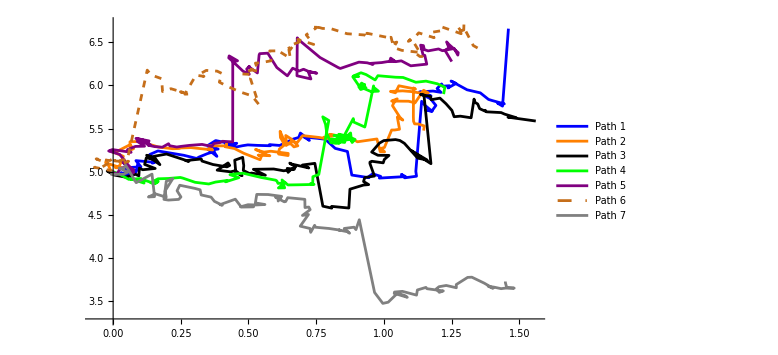

```mathematica
Result5=ListLinePlot[{Tr11,Tr22,Tr33,Tr44,Tr55,Tr66,Tr77},AxesLabel->{Style["",Bold,Black],Style["",Bold,Black]},LabelStyle->Directive[Bold,Medium],
PlotRange->All,ImageSize->Large, PlotStyle->{Blue,Orange,Black,Green,Purple,Dashed,Gray},PlotLegends->Placed[{Style["Path 1",Bold,Black],Style["Path 2",Bold,Black],Style["Path 3",Bold,Black],Style["Path 4",Bold,Black],Style["Path 5",Bold,Black],Style["Path 6",Bold,Black],Style["Path 7",Bold,Black]},Right],Epilog->{Red,Thick,Line[{{0,1},{10,1}}]}]
```

```mathematica
Export["C:\\Users\\Juan Sebastian\\Documents\\Cinvestav\\Tesis\\Tesis\\stochastic differential equations\\Velocidades\\Grafica parametrica, l=1,m=0\\Graficas\\Graficas sin unidades\\Variando omega0\\omega 10000\\r vs t\\grafica2(7trayec-25s).PNG",Result5,"PNG",ImageResolution->300];
```

```mathematica
(*+Sqrt[2 σ] ⅆw1[t]*)
```